# Sphere Irradiance

Here we’re investigating a way to reduce the complexity of computing the irradiance provided by a sphere from a specific position outside the sphere. The point has a position and a normal and we’re especially interested in handling the horizon clipping situation.
The original analytical solution comes from Snyder, J. 1996 “Area Light Sources for Real-Time Graphics” (https://www.microsoft.com/en-us/research/publication/area-light-sources-for-real-time-graphics/).
It was later optimized by Sébastien Lagarde then analytically fitted by Stephen Hill and Eric Heitz but the fitting suffers from serious issues when the sphere goes below the horizon.

We thus need to find a better approximation!

Code

// Ref: Moving Frostbite to Physically Based Rendering, page 47 (2015, optimized).
// ‘sinSqSigma’ is the sine^2 of the real of the opening angle of the sphere as seen from the shaded point.
// ‘cosOmega’ is the cosine of the angle between the normal and the direction to the center of the light.
// N.b.: this function accounts for horizon clipping.
real DiffuseSphereLightIrradiance(real sinSqSigma, real cosOmega)
{
	real cosSqOmega = cosOmega * cosOmega;                     // y^2

	if (cosSqOmega > sinSqSigma)                                // (y^2)>x
            	return saturate(sinSqSigma * cosOmega);                 // Clip[x*y,{0,1}]
        	else
        	{
            real cotSqSigma = rcp(sinSqSigma) - 1;                 // 1/x-1
            real tanSqSigma = rcp(cotSqSigma);                     // x/(1-x)
            real sinSqOmega = 1 - cosSqOmega;                      // 1-y^2

            real w = sinSqOmega * tanSqSigma;                      // (1-y^2)*(x/(1-x))
            real x = -cosOmega * rsqrt(w);                         // -y*Sqrt[(1/x-1)/(1-y^2)]
            real y = sqrt(sinSqOmega * tanSqSigma - cosSqOmega);   // Sqrt[(1-y^2)*(x/(1-x))-y^2]
            real z = y * cotSqSigma;                               // Sqrt[(1-y^2)*(x/(1-x))-y^2]*(1/x-1)

            real a = cosOmega * acos(x) - z;                       // y*ArcCos[-y*Sqrt[(1/x-1)/(1-y^2)]]-Sqrt[(1-y^2)*(x/(1-x))-y^2]*(1/x-1)
            real b = atan(y);                                      // ArcTan[Sqrt[(1-y^2)*(x/(1-x))-y^2]]

            return saturate(INV_PI * (a * sinSqSigma + b));
        }
}

Function

```mathematica
irradiance:=Function[{cosOmega,sqSinSigma},
(*sqCosOmega = cosOmega*cosOmega;
sqSinOmega=1-sqCosOmega;
sqCosSigma=1-sqSinSigma;
sqTanSigma = sqSinSigma / sqCosSigma;
σ=ArcSin[√sqSinSigma];
sqTanSigma=Tan[σ]^2;

w=sqSinOmega * sqTanSigma;
x=-cosOmega/(√w);
y=√(sqSinOmega*sqTanSigma-sqCosOmega);
z=y/sqTanSigma;
*)

ω=ArcCos[cosOmega];
σ=Min[π/2-0.000001,ArcSin[√Min[1,sqSinSigma]]];
w=Sin[ω]*Tan[σ];
x=(-Cos[ω])/w;
y=√(w*w-Cos[ω]^2);
z=y/Tan[σ]^2;

a=Cos[ω]*ArcCos[x]-z;
b=ArcTan[y];

result=If[Cos[ω]^2>Sin[σ]^2,
 Sin[σ]^2*Cos[ω], (* Clip[x*y,{0,1}] *)
(Sin[σ]^2*a+b)/π
];
Clip[ Re[result],{0,1}]
]
irradiance[Cos[π/4],Sin[π/8]^2]
irradiance[Cos[π/4],10]
```

Sin[π/8]^2/(√2)

0.853553

```mathematica
Plot3D[irradiance[Cos[θ],Sin[σ]^2],{θ,0,π},{σ,0,π/2}]
```

-Graphics3D-

```mathematica
Plot3D[irradiance[Cosθ,SqSinσ],{Cosθ,1,-1},{SqSinσ,0,1},PlotRange->{0,1}]
```

-Graphics3D-

Current Approximation

```mathematica
irradianceApprox1:=Function[{cosOmega,sqSinSigma},
x=sqSinSigma;
y=cosOmega;
x*(0.9245867471551246+y)*(0.5+(-0.9245867471551246+y)*(0.5359050373687144+x*(-1.0054221851257754+x*(1.8199061187417047-x*1.3172081704209504))))
]
```

```mathematica
Plot3D[irradianceApprox1[Cos[θ],Sin[σ]^2],{θ,0,π},{σ,0,π/2}]
```

-Graphics3D-

```mathematica
Show[Plot3D[irradiance[Cos[θ],Sin[σ]^2],{θ,0,π},{σ,0,π/2},PlotRange->{-0.1,1}],Plot3D[irradianceApprox1[Cos[θ],Sin[σ]^2],{θ,0,π},{σ,0,π/2},PlotStyle->Red]]
```

-Graphics3D-

New Fitting

The following plot is almost a bilinear interpolation when x=Cos(θ) and y=(Sin(σ))^2:

```mathematica
Plot3D[irradiance[Cosθ,SqSinσ],{Cosθ,-1,1},{SqSinσ,0,1},PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
(*ta=Flatten[Table[{CosTheta,SqSinSigma,irradiance[CosTheta,SqSinSigma]},{CosTheta,-1,0.98,0.02},{SqSinSigma,0,0.99,0.01}],1];*)
ta=Flatten[Table[{(1+CosTheta)/2,SqSinSigma,irradiance[CosTheta,SqSinSigma]},{CosTheta,-0.9,0.9,0.2},{SqSinSigma,0,0.9,0.1}],1];
ta=Flatten[Table[{(1+CosTheta)/2,SqSinSigma,irradiance[CosTheta,SqSinSigma]},{CosTheta,-0.99,1,0.02},{SqSinSigma,0,0.999,0.01}],1];

(* Actual table *)
(*ta=Flatten[Table[{CosTheta,SqSinSigma,irradiance[CosTheta,SqSinSigma]},{CosTheta,-0.99,0.99,0.05},{SqSinSigma,0,0.98,0.02}],1];*)

Length[ta]
```

10000

```mathematica
ListPlot3D[ta,PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
Clear[a,b,c,d,e,x,y]

(*fit=NonlinearModelFit[ta,model,{a,b,c,d,e},{x,y}];*)
(*Normal[fit]*)

model=a+b*x+c*y+d*x*y;
model=y*(x+e)*(0.5+(x-e)*(a+b*y+c*y^2+d*y^3)); (* Heitz Model *)
model=y*(1+x)/2*(a+b*(1+x)/2+c*y+d*(1+x)/2*y);
model=a*(1+x)/2*y+b*((1+x)/2)^2*y+c*(1+x)/2*y^2+d*((1+x)/2)^2*y^2;
model=a*x*y+b*x^2*y+c*x*y^2+d*x^2*y^2;

fit=FindFit[ta,model,{a,b,c,d,e},{x,y}]
irradianceApprox2=Function[{x,y},Evaluate[model/.fit]]

Normal[NonlinearModelFit[ta,model,{a,b,c,d,e},{x,y}]]

(*fit={a->-1,b->2,c->π/2,d->-π/2}*)

(*Show[Plot3D[model/.fit,{x,-1,1},{y,0,1},PlotRange->All,AxesLabel->{"x","y"}],ListPointPlot3D[ta,PlotStyle->Directive[PointSize[Medium],Red]]]*)
Show[Plot3D[irradianceApprox2[x,y],{x,0,1},{y,0,1},PlotRange->All,AxesLabel->{"x","y"}],
ListPointPlot3D[ta,PlotStyle->Directive[PointSize[Tiny],Red]]]
```

{a→-1.05247,b→2.08825,c→1.54768,d→-1.60201,e→0.}

Function[{x,y},-1.05247 x y+2.08825 x^2 y+1.54768 x y^2-1.60201 x^2 y^2]

-1.05247 x y+2.08825 x^2 y+1.54768 x y^2-1.60201 x^2 y^2

-Graphics3D-

```mathematica
Show[Plot3D[irradiance[Cosθ,SqSinσ],{Cosθ,-1,1},{SqSinσ,0,1},PlotRange->All,AxesLabel->{"Cos(θ)","Sin^2(σ)","Irradiance"}],
Plot3D[irradianceApprox1[Cosθ,SqSinσ],{Cosθ,-1,1},{SqSinσ,0,1},PlotStyle->Red],
Plot3D[irradianceApprox2[(1+Cosθ)/2,SqSinσ],{Cosθ,-1,1},{SqSinσ,0,1},PlotStyle->Green]
]
```

-Graphics3D-

```mathematica
Show[Plot3D[irradiance[Cos[θ],Sin[σ]^2],{θ,0,π},{σ,0,π/2},PlotRange->{-0.1,1}],
Plot3D[irradianceApprox1[Cos[θ],Sin[σ]^2],{θ,0,π},{σ,0,π/2},PlotStyle->Red],
Plot3D[irradianceApprox2[(1+Cos[θ])/2,Sin[σ]^2],{θ,0,π},{σ,0,π/2},PlotStyle->Green]]
```

-Graphics3D-

```mathematica
(0.9199900928436545+x) y (0.5+(-0.9199900928436545+x) (0.5233563050176789-0.905795873194072 y+1.6168821730086278 y^2-1.197654337001554 y^3))
```

Even Newer Fitting

We noticed at runtime that problematica values are the ones where Sin[σ]^2 is close to 1. We need to take extra care close to these values.

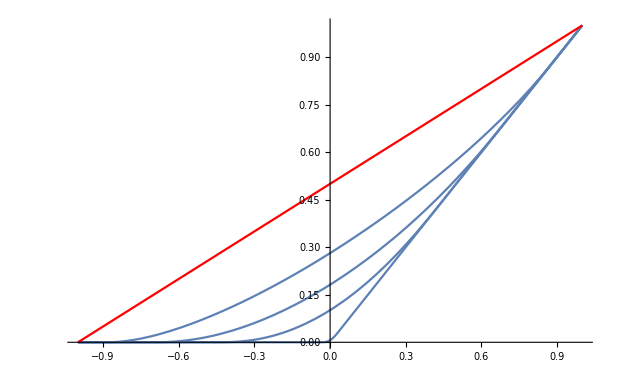

```mathematica
Show[Plot[irradiance[CosTheta,0.001]/0.001,{CosTheta,-1,1}],
Plot[irradiance[CosTheta,0.2]/0.2,{CosTheta,-1,1}],
Plot[irradiance[CosTheta,0.5]/0.5,{CosTheta,-1,1}],
Plot[irradiance[CosTheta,0.8]/0.8,{CosTheta,-1,1}],
Plot[irradiance[CosTheta,1],{CosTheta,-1,1},PlotStyle->Red]
]
```

```mathematica
test=Function[{x,y},
Max[0,(x+y)/(1+y)]
];
Manipulate[Plot[test[x,a],{x,-1,1},PlotRange->{0,1}],{a,0,1}]
```

```mathematica
Show[
Plot3D[irradiance[x,y],{x,-1,1},{y,0,1}],
Plot3D[test[x,y-0.2]*y,{x,-1,1},{y,0,1},PlotStyle->Red]
]
```

-Graphics3D-

```mathematica
diff[x_,y_]:=N[Re[irradiance[x,y]]]-N[Re[test[x,y-0.2]*y]];
Plot3D[diff[x,y],{x,-1,1},{y,0,1}]
```

-Graphics3D-

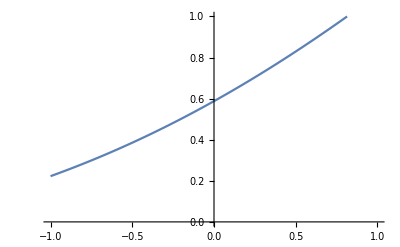

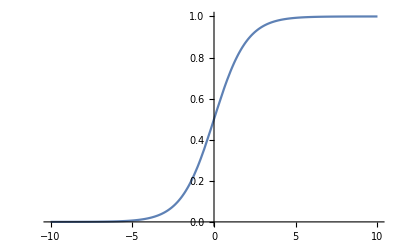

```mathematica
Plot[Log[0.8+Exp[0.8*x]],{x,-1,1},PlotRange->{0,1}]
Plot[Exp[x]/(1+Exp[x]),{x,-10,10},PlotRange->{0,1}]
```

Soft reLu

```mathematica
softreLU[x_,a_]:=1+Log[(ⅇ^(a*x)+1)/(ⅇ^a+1)]/a;
Manipulate[Plot[softreLU[x,a],{x,-1,1},PlotRange->{0,1}],{a,0.001,100}]
```

```mathematica
softreLU2[x_,y_,a_]:=y*softreLU[x,a];
Manipulate[Plot3D[softreLU2[x,y,a],{x,-1,+1},{y,0,1},PlotRange->{0,1}],{a,0.001,20}]
```

Even Even Newer Fitting

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

17

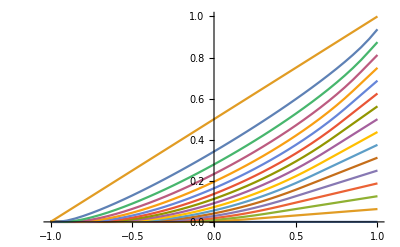

```mathematica
ta=Table[{CosTheta,irradiance[CosTheta,SqSinSigma]},{SqSinSigma,0,1,0.0625},{CosTheta,-1,1,0.05}];
Length[ta]
Show[ListLinePlot[ta,PlotRange->{0,1}]]
```

```mathematica
Clear[x,y,a,b,c,d,e]
index=11;
y=0.0625*index;
model=y*(1+Log[(1+ⅇ^(a x))/(1+ⅇ^a)]/a);
model=y*(1+(Log[1+Exp[a*x]]-Log[1+Exp[a]])/a);
model=softreLU2[x,y,a];
(*NonlinearModelFit[ta[[index]],{model,{a>0}},{a,b,c,d,e},x]*)
FindFit[ta[[index]],{model,{a>0}},{a},x]

(*fit=FindFit[ta[[2]],{model,{a>0}},{a,b,c,d,e},{x,y}]
irradianceApprox2=Function[{x},Evaluate[model/.fit]]*)
```

{a→3.84929}

```mathematica
Clear[a,x,y]
index=0;
FindFit[ta[[1+index]],{model/.y-> 0.0625*index,{a>0}},{a},x]
```

{a→54.8005}

```mathematica
Clear[a,x,y]
fits=Table[a/.FindFit[ta[[1+index]],{model/.y-> 0.0625*index,{a>0}},{a},x],{index,0,Length[ta]-1}]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.33021×10^-8, 5.40646×10^-6, 1.34365×10^-8}, is returned.

{54.8005,52.367,46.9361,34.2208,24.2888,17.204,12.4914,9.29156,6.95717,5.18887,3.84929,2.82976,2.01168,1.29574,0.592661,1.24065×10^-6,5.86338×10^-13}

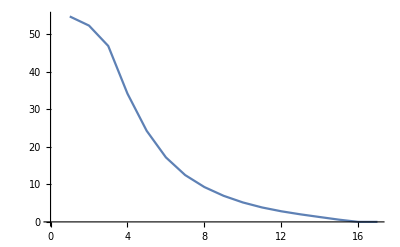

```mathematica
ListLinePlot[fits]
```